```mathematica
Plot3D[Sin[x]Sin[y],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

There' s no such thing as "cheating", there' s just using the appropriate tools.  When using Mathematica, it will smash through calculations, but totally ignore any errors you put in the setup. So you need to be careful and test limits and known solutions, just like always.

```mathematica
z[x_,y_]:=Sin[x]Sin[y]
D[z[x,y[x]],x]
```

Cos[x] Sin[y[x]]+Cos[y[x]] Sin[x] y'[x]

```mathematica
f=Sqrt[1+y'[x]^2+D[z[x,y[x]],x]^2]
```

√(1+y'[x]^2+(Cos[x] Sin[y[x]]+Cos[y[x]] Sin[x] y'[x])^2)

```mathematica
ELeqn=FullSimplify[D[D[f,y'[x]],x]-D[f,y[x]]]==0
```

(-2 Sin[x]^2 Sin[2 y[x]]+(3+Cos[2 y[x]]) Sin[2 x] y'[x]-(3+Cos[2 x]) Sin[2 y[x]] y'[x]^2+4 Cos[x] Sin[x] Sin[y[x]]^2 y'[x]^3+(6-2 Cos[2 x] Cos[2 y[x]]) y''[x])/(4 (1+y'[x]^2+(Cos[x] Sin[y[x]]+Cos[y[x]] Sin[x] y'[x])^2)^(3/2))==0

Just looking at that, obviously it' s not going to have an analytic solution.  Let' s solve it numerically.

```mathematica
soln[y0_,vy0_,xmax_]:=NDSolve[{ELeqn,y[0]==y0,y'[0]==vy0},y,{x,0,xmax}]
```

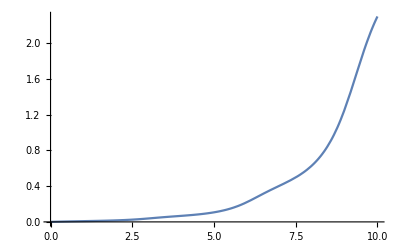

```mathematica
Plot[Evaluate[y[x]/.soln[0,0.01,10]],{x,0,10}]
```

```mathematica
line[y0_,vy0_,xmax_]:={x,y[x],z[x,y[x]]}/.soln[y0,vy0,xmax][[1]]
```

```mathematica
Manipulate[ParametricPlot3D[{Evaluate[line[y0,vy,20]],{x,yy,z[x,yy]}},{x,0,20},{yy,-10,10},PlotStyle->{Directive[Green,Thickness[0.25]],Yellow},Background->Gray,Boxed->False,PlotRange->All],{{y0,.01},0,0.3},{{vy,-0.01},-0.1,0.1}]
```